```mathematica
f[x_,mu_,s_]:=1/Sqrt[2*Pi*s^2]Exp[-(x-mu)^2/2/s^2]
```

```mathematica
Series[Exp[-(x-mu)^2/2/s^2],{mu,0,6}];
```

```mathematica
%7
```

(ⅇ^(-x^2/(2 s^2)))/(√(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) x mu)/(√(2 π) (s^2)^(3/2))-((ⅇ^(-x^2/(2 s^2)) (s^2-x^2)) mu^2)/(2 (√(2 π) s^4 √(s^2)))+(ⅇ^(-x^2/(2 s^2)) (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)) mu^3)/(3 √(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)) mu^4)/(4 √(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) (-(-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2))/(3 s^2)+(x (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)))/(4 s^2)) mu^5)/(5 √(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) (-(-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2))/(4 s^2)+(x (-(-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2))/(3 s^2)+(x (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)))/(4 s^2)))/(5 s^2)) mu^6)/(6 √(2 π) √(s^2))+O[mu]^7

```mathematica
Simplify[CoefficientList[%11,mu]]
```

{ⅇ^(-x^2/(2 s^2)),(ⅇ^(-x^2/(2 s^2)) x)/s^2,(ⅇ^(-x^2/(2 s^2)) (-s^2+x^2))/(2 s^4),(ⅇ^(-x^2/(2 s^2)) (-3 s^2 x+x^3))/(6 s^6),(ⅇ^(-x^2/(2 s^2)) (3 s^4-6 s^2 x^2+x^4))/(24 s^8),(ⅇ^(-x^2/(2 s^2)) x (15 s^4-10 s^2 x^2+x^4))/(120 s^10),(ⅇ^(-x^2/(2 s^2)) (-15 s^6+45 s^4 x^2-15 s^2 x^4+x^6))/(720 s^12)}

(ⅇ^(-x^2/(2 s^2)))/(√(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) x mu)/(√(2 π) (s^2)^(3/2))-((ⅇ^(-x^2/(2 s^2)) (s^2-x^2)) mu^2)/(2 (√(2 π) s^4 √(s^2)))+(ⅇ^(-x^2/(2 s^2)) (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)) mu^3)/(3 √(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)) mu^4)/(4 √(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) (-(-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2))/(3 s^2)+(x (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)))/(4 s^2)) mu^5)/(5 √(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) (-(-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2))/(4 s^2)+(x (-(-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2))/(3 s^2)+(x (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)))/(4 s^2)))/(5 s^2)) mu^6)/(6 √(2 π) √(s^2))+O[mu]^7

```mathematica
fs[x_,mu_,s_]:=(ⅇ^(-x^2/(2 s^2)))/(√(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) x mu)/(√(2 π) (s^2)^(3/2))-((ⅇ^(-x^2/(2 s^2)) (s^2-x^2)) mu^2)/(2 (√(2 π) s^4 √(s^2)))+(ⅇ^(-x^2/(2 s^2)) (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)) mu^3)/(3 √(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)) mu^4)/(4 √(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) (-(-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2))/(3 s^2)+(x (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)))/(4 s^2)) mu^5)/(5 √(2 π) √(s^2))+(ⅇ^(-x^2/(2 s^2)) (-(-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2))/(4 s^2)+(x (-(-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2))/(3 s^2)+(x (-(-1/s^2+x^2/s^4)/(2 s^2)+(x (-x/s^4+(x (-1/s^2+x^2/s^4))/(2 s^2)))/(3 s^2)))/(4 s^2)))/(5 s^2)) mu^6)/(6 √(2 π) √(s^2))
```

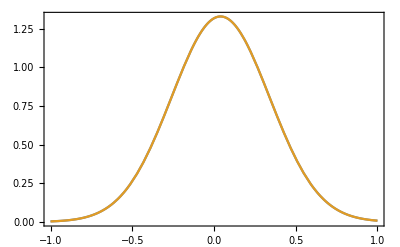

```mathematica
(* exp(-(x-0.04)^2/2/0.3^2 *)
Plot[{f[x,0.04,0.3],fs[x,0.04,0.3]},{x,-1,1},Frame->True]
```

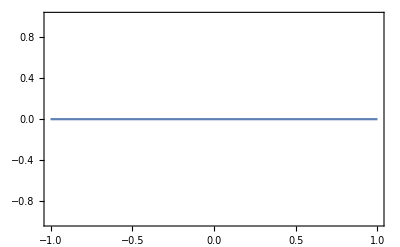

```mathematica
Plot[fs[x,0.04,0.3]-fs[x,0.04,0.3],{x,-1,1},Frame->True]
```

```mathematica
a = 0;
st = -2;
ed = 2;
num = 20000;
dx = (ed - st)/num;
For[i=0,i<num,i++,a = a +(f[st+dx*i,0,0.3] + f[st+dx*(i+1),0,0.3])*dx/2];
Print[a];
Print[Integrate[f[x,0,0.3],{x,-2,2}]];
```

1.

1.

```mathematica
Simplify[CoefficientList[%149,mu]]
```

{ⅇ^(-x^2/(2 s^2)),(ⅇ^(-x^2/(2 s^2)) x)/s^2,(ⅇ^(-x^2/(2 s^2)) (-s^2+x^2))/(2 s^4),(ⅇ^(-x^2/(2 s^2)) (-3 s^2 x+x^3))/(6 s^6),(ⅇ^(-x^2/(2 s^2)) (3 s^4-6 s^2 x^2+x^4))/(24 s^8),(ⅇ^(-x^2/(2 s^2)) x (15 s^4-10 s^2 x^2+x^4))/(120 s^10),(ⅇ^(-x^2/(2 s^2)) (-15 s^6+45 s^4 x^2-15 s^2 x^4+x^6))/(720 s^12)}

```mathematica
fs[0,0.04,0.3]
```

General::ivar: 0.04 不是一个有效的变量.

```mathematica
Series[1.3180394696193922,{0.04,0,6}]68.3028593-0.0150074-0.0150074
```

```mathematica
Solve[w1*s1+(1-w1)*s2==-0.0151&& w1*s1^2+(1-w1)*s2^2==0.00018935 && w1*s1^3+(1-w1)*s2^3==-0.00007543&&w1>0,{w1,s1,s2}]
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

{{w1→1.00001,s1→-0.0150797,s2→1.89223}}

```mathematica
Solve[w1*s1+(1-w1)*s2==26.9811166&& w1*s1^2+(1-w1)*s2^2==-0.0142067&& w1*s1^3+(1-w1)*s2^3==-0.0142067,{w1,s1,s2}]
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

{{w1→0.5-587.806 ⅈ,s1→-0.000253509+0.0229509 ⅈ,s2→-0.000253509-0.0229509 ⅈ},{w1→0.5+587.806 ⅈ,s1→-0.000253509-0.0229509 ⅈ,s2→-0.000253509+0.0229509 ⅈ}}

```mathematica
A[g1_,g2_]:=a1 + a2*g1+a3*g2+a4*g1^2+a5*g2^2;
B[g1_,g2_]:=b1 + b2*g1+b3*g2 +b4*g1^2+b5*g2^2;
G[g1_,g2_]:=A/B;
```

```mathematica
A[1,2]
```

a1+a2+2 a3+a4+4 a5

```mathematica
Information[A]
```

```mathematica
Series[(a1 + a2*g1+a3*g2+a4*g1^2+a5*g2^2)/(b1 + b2*g1+b3*g2 +b4*g1^2+b5*g2^2),{g1,0,2},{g2,0,2}]
```

(a1/b1+((a3 b1-a1 b3) g2)/b1^2+((a5 b1^2-a3 b1 b3+a1 b3^2-a1 b1 b5) g2^2)/b1^3+O[g2]^3)+((a2 b1-a1 b2)/b1^2+((-a3 b1 b2-a2 b1 b3+2 a1 b2 b3) g2)/b1^3+((a2 (b3^2-b1 b5))/b1^3-(b2 (a5 b1^2-2 a3 b1 b3+3 a1 b3^2-2 a1 b1 b5))/b1^4) g2^2+O[g2]^3) g1+((a4 b1^2-a2 b1 b2+a1 b2^2-a1 b1 b4)/b1^3+((a3 b1 b2^2-a4 b1^2 b3+2 a2 b1 b2 b3-3 a1 b2^2 b3-a3 b1^2 b4+2 a1 b1 b3 b4) g2)/b1^4+(-b3 (a3/b1^3-(3 a1 b3)/b1^4) b4-(a1 b4 b5)/b1^3+(a4 (b3^2-b1 b5))/b1^3+(a2 b2 (-3 b3^2+2 b1 b5))/b1^4+(b2^2-b1 b4) (a5/b1^3-(3 a3 b3)/b1^4-(3 a1 (-2 b3^2+b1 b5))/b1^5)) g2^2+O[g2]^3) g1^2+O[g1]^3

```mathematica
CoefficientList[%11,g1]
```

{a1/b1+((a3 b1-a1 b3) g2)/b1^2+((a5 b1^2-a3 b1 b3+a1 b3^2-a1 b1 b5) g2^2)/b1^3+(-(a5 b3)/b1^2+(a3 (b3^2-b1 b5))/b1^3+(a1 (-b3^3+2 b1 b3 b5))/b1^4) g2^3,(a2 b1-a1 b2)/b1^2+((-a3 b1 b2-a2 b1 b3+2 a1 b2 b3) g2)/b1^3+((a2 (b3^2-b1 b5))/b1^3-(b2 (a5 b1^2-2 a3 b1 b3+3 a1 b3^2-2 a1 b1 b5))/b1^4) g2^2+((a2 (-b3^3+2 b1 b3 b5))/b1^4+(b2 (2 a5 b1^2 b3-3 a3 b1 b3^2+4 a1 b3^3+2 a3 b1^2 b5-6 a1 b1 b3 b5))/b1^5) g2^3,(a4 b1^2-a2 b1 b2+a1 b2^2-a1 b1 b4)/b1^3+((a3 b1 b2^2-a4 b1^2 b3+2 a2 b1 b2 b3-3 a1 b2^2 b3-a3 b1^2 b4+2 a1 b1 b3 b4) g2)/b1^4+(-b3 (a3/b1^3-(3 a1 b3)/b1^4) b4-(a1 b4 b5)/b1^3+(a4 (b3^2-b1 b5))/b1^3+(a2 b2 (-3 b3^2+2 b1 b5))/b1^4+(b2^2-b1 b4) (a5/b1^3-(3 a3 b3)/b1^4-(3 a1 (-2 b3^2+b1 b5))/b1^5)) g2^2+1/b1^6(-3 a5 b1^2 b2^2 b3+6 a3 b1 b2^2 b3^2-a4 b1^2 b3^3+4 a2 b1 b2 b3^3-10 a1 b2^2 b3^3+2 a5 b1^3 b3 b4-3 a3 b1^2 b3^2 b4+4 a1 b1 b3^3 b4-3 a3 b1^2 b2^2 b5+2 a4 b1^3 b3 b5-6 a2 b1^2 b2 b3 b5+12 a1 b1 b2^2 b3 b5+2 a3 b1^3 b4 b5-6 a1 b1^2 b3 b4 b5) g2^3,-(a4 b2)/b1^2+(a2 (b2^2-b1 b4))/b1^3+(a1 (-b2^3+2 b1 b2 b4))/b1^4+((-a3 b1 b2^3+2 a4 b1^2 b2 b3-3 a2 b1 b2^2 b3+4 a1 b2^3 b3+2 a3 b1^2 b2 b4+2 a2 b1^2 b3 b4-6 a1 b1 b2 b3 b4) g2)/b1^5+(2 b2 b3 (a3/b1^4-(4 a1 b3)/b1^5) b4+(2 a1 b2 b4 b5)/b1^4+(a4 b2 (-3 b3^2+2 b1 b5))/b1^4+(a2 (6 b2^2 b3^2-3 b1 b3^2 b4-3 b1 b2^2 b5+2 b1^2 b4 b5))/b1^5+(-b2^3+2 b1 b2 b4) (a5/b1^4-(4 a3 b3)/b1^5-(2 a1 (-5 b3^2+2 b1 b5))/b1^6)) g2^2+(-(2 a4 b2 b3 (-2 b3^2+3 b1 b5))/b1^5-(2 a2 b3 (5 b2^2 b3^2-2 b1 b3^2 b4-6 b1 b2^2 b5+3 b1^2 b4 b5))/b1^6+1/b1^7 2 (2 a5 b1^2 b2^3 b3-5 a3 b1 b2^3 b3^2+10 a1 b2^3 b3^3-3 a5 b1^3 b2 b3 b4+6 a3 b1^2 b2 b3^2 b4-10 a1 b1 b2 b3^3 b4+2 a3 b1^2 b2^3 b5-10 a1 b1 b2^3 b3 b5-3 a3 b1^3 b2 b4 b5+12 a1 b1^2 b2 b3 b4 b5)) g2^3}

```mathematica
Series[((1+g1^2+g2^2-2*g1)*x^2+(1+g1^2+g2^2+2*g1)*y^2-4*g2*x*y)^((1-2*n)/2*n),{g1,0,1},{g2,0,1}]
```

((x^2+y^2)^(1/2 (1-2 n) n)-2 ((1-2 n) n x y (x^2+y^2)^(-1+1/2 (1-2 n) n)) g2+O[g2]^2)+(n (-1+2 n) (x^2-y^2) (x^2+y^2)^(-1+1/2 (1-2 n) n)+2 n (-1+2 n) (2-n+2 n^2) x y (x^2-y^2) (x^2+y^2)^(-2+1/2 (1-2 n) n) g2+O[g2]^2) g1+O[g1]^2